```mathematica
Guy F. Mongelli                                                                                  2/15/2013;
Prof. R.M. Sankaran                                                                      ECHE 462;
```

```mathematica
Problem Set #3;
```

```mathematica
Problem#1;
```

```mathematica
Since the parallel reactions are irreversible, the reactions selectivity will be completely dependent upon kinetic effects.  In other words, the reactions are competing and how much is formed of each product depends on the relative rates of consumption of the shared reactant.The reactions are written:
```

```mathematica
A(->)^Subscript[k, 1] B+C
```

```mathematica
A(->)^Subscript[k, 2] D+E
```

```mathematica
If 2-propanol is labelled species A, acetone is species B, hydrogen gas is species C,propene is species D, and water species E- then, the rate of change in the disappearance of species A can be written:
```

```mathematica
Subscript[dc, A]/dt=-Subscript[k, 1]*Subscript[c, A]-Subscript[k, 2]*Subscript[c, A]
```

```mathematica
The rate of formation of B is:
```

```mathematica
Subscript[dc, B]/dt=Subscript[k, 1]*Subscript[c, A]
```

```mathematica
The rate of formation of C is:
```

```mathematica
Subscript[dc, D]/dt=Subscript[k, 2]*Subscript[c, A]
```

```mathematica
What is given in the table within the problem statement is (Subscript[dc, B]/dt).
```

```mathematica
Let the initial concentration 2-propanol be:
```

```mathematica
cA0=1 (* mol/L *);
```

```mathematica
Subscript[k, 1] and Subscript[k, 2] are temperature dependent and therefore write them as:
```

```mathematica
Subscript[k, 1][T_]=kA0*Exp[-Ea/R*T];
```

```mathematica
Subscript[k, 2][T_]=kB0*Exp[-Eb/R*T];
```

```mathematica
Then solve the Subscript[c, A] equation with the included temperature dependence:
```

```mathematica
DSolve[{cA'[t]== -Subscript[k, 1][T]*cA[t]-Subscript[k, 2][T]*cA[t],cA[0]==1},cA[t],t]
```

{{cA[t]→ⅇ^(-ⅇ^(-(Ea T)/R-(Eb T)/R) (ⅇ^((Eb T)/R) kA0+ⅇ^((Ea T)/R) kB0) t)}}

```mathematica
cA[t_]=ⅇ^(-ⅇ^(-(Ea T)/R-(Eb T)/R) (ⅇ^((Eb T)/R) kA0+ⅇ^((Ea T)/R) kB0) t);
```

```mathematica
So what is given in the table is (Subscript[dc, B]/dt).  Next solve that relation with knowledge of cA[t]:
```

```mathematica
Clear[cB]
```

```mathematica
DSolve[{cB'[t]== Subscript[k, 1][T]*cA[t],cB[0]==0},cB[t],t]
```

{{cB[t]→(ⅇ^(-(ⅇ^(-(Ea T)/R) kA0+ⅇ^(-(Eb T)/R) kB0) t+(Eb T)/R) (-1+ⅇ^((ⅇ^(-(Ea T)/R) kA0+ⅇ^(-(Eb T)/R) kB0) t)) kA0)/(ⅇ^((Eb T)/R) kA0+ⅇ^((Ea T)/R) kB0)}}

```mathematica
FullSimplify[(ⅇ^(-(ⅇ^(-(Ea T)/R) kA0+ⅇ^(-(Eb T)/R) kB0) t+(Eb T)/R) (-1+ⅇ^((ⅇ^(-(Ea T)/R) kA0+ⅇ^(-(Eb T)/R) kB0) t)) kA0)/(ⅇ^((Eb T)/R) kA0+ⅇ^((Ea T)/R) kB0)]
```

-(ⅇ^((Eb T)/R) (-1+ⅇ^(-ⅇ^(-(Ea T)/R) kA0 t-ⅇ^(-(Eb T)/R) kB0 t)) kA0)/(ⅇ^((Eb T)/R) kA0+ⅇ^((Ea T)/R) kB0)

```mathematica
cB[t_]=-(ⅇ^((Eb T)/R) (-1+ⅇ^(-ⅇ^(-(Ea T)/R) kA0 t-ⅇ^(-(Eb T)/R) kB0 t)) kA0)/(ⅇ^((Eb T)/R) kA0+ⅇ^((Ea T)/R) kB0);
```

```mathematica
FullSimplify[D[cB[t],t]]
```

ⅇ^(-(ⅇ^(-(Ea T)/R) kA0 R t+ⅇ^(-(Eb T)/R) kB0 R t+Ea T)/R) kA0

```mathematica
DSolve[{cD'[t]== Subscript[k, 2][T]*cA[t],cD[0]==0},cD[t],t]
```

{{cD[t]→(ⅇ^(-(ⅇ^(-(Ea T)/R) kA0+ⅇ^(-(Eb T)/R) kB0) t+(Ea T)/R) (-1+ⅇ^((ⅇ^(-(Ea T)/R) kA0+ⅇ^(-(Eb T)/R) kB0) t)) kB0)/(ⅇ^((Eb T)/R) kA0+ⅇ^((Ea T)/R) kB0)}}

```mathematica
FullSimplify[(ⅇ^(-(ⅇ^(-(Ea T)/R) kA0+ⅇ^(-(Eb T)/R) kB0) t+(Ea T)/R) (-1+ⅇ^((ⅇ^(-(Ea T)/R) kA0+ⅇ^(-(Eb T)/R) kB0) t)) kB0)/(ⅇ^((Eb T)/R) kA0+ⅇ^((Ea T)/R) kB0)]
```

-(ⅇ^((Ea T)/R) (-1+ⅇ^(-ⅇ^(-(Ea T)/R) kA0 t-ⅇ^(-(Eb T)/R) kB0 t)) kB0)/(ⅇ^((Eb T)/R) kA0+ⅇ^((Ea T)/R) kB0)

```mathematica
cD[t_]=-(ⅇ^((Ea T)/R) (-1+ⅇ^(-ⅇ^(-(Ea T)/R) kA0 t-ⅇ^(-(Eb T)/R) kB0 t)) kB0)/(ⅇ^((Eb T)/R) kA0+ⅇ^((Ea T)/R) kB0);
```

```mathematica
FullSimplify[D[cD[t],t]]
```

ⅇ^(-(ⅇ^(-(Ea T)/R) kA0 R t+ⅇ^(-(Eb T)/R) kB0 R t+Eb T)/R) kB0

```mathematica
data1={{573,4.1*10^-7},{583,7.0*10^-7},{594,1.4*10^-6},{603,2.2*10^-6},{612,3.6*10^-6}};
```

```mathematica
Fit the data given to determine the kA0 and Ea.
```

```mathematica
R=8.3144; (*J/mol-k *)
```

```mathematica
nlm=NonlinearModelFit[data1,k01*Exp[-Ea/(R*T)],{k01,Ea},T]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[7.48829×10^6 ⅇ^(-17383./T)]

```mathematica
Clear[Ea]
```

```mathematica
kA0=7.52*10^6;
Ea=17383(*J/mol*);
```

```mathematica
plotb=ListPlot[{data1},PlotRange->{0,5*10^-6},AxesLabel->{"Temp(K)","dc_B/dt (mol/gcat/s)"}];
```

```mathematica
plota=Plot[7.521559964397838*^6 ⅇ^(-17385.69120872715/T),{T,565,615}];
```

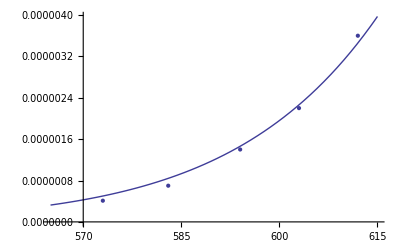

```mathematica
Show[plota,plotb]
```

```mathematica
The follwoing data set contains the solectivity to acetone as a function of temperature.
```

```mathematica
data2={{573,92},{583,86},{594,81},{603,81},{612,81}};
```

```mathematica
nlm2=NonlinearModelFit[data2,a*T^2+b*T+c,{a,b,c},T]
```

FittedModel[4502.31-14.6424 T+0.0121215 T^2]

```mathematica
Sel[T_]=4502.305302780317-14.642425858257704 T+0.012121521887891807 T^2;
```

```mathematica
plot3=ListPlot[{data2},PlotRange->{0,100},AxesLabel->{"Temp(K)","Selectivity to Acetone (%)"}];
```

```mathematica
plot4=Plot[4502.305302780317-14.642425858257704 T+0.012121521887891807 T^2,{T,575,615},PlotRange->{0,100}];
```

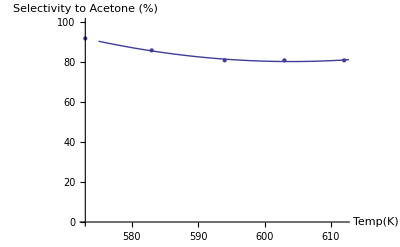

```mathematica
Show[plot3,plot4]
```

```mathematica
cB[t]
```

-(7.52×10^6 ⅇ^(0.120273 Eb T) (-1+ⅇ^(-7.52×10^6 ⅇ^(-2090.71 T) t-7.52×10^6 ⅇ^(-0.120273 Eb T) t)))/(7.52×10^6 ⅇ^(2090.71 T)+7.52×10^6 ⅇ^(0.120273 Eb T))

```mathematica
cD[t]
```

-(7.52×10^6 ⅇ^(2090.71 T) (-1+ⅇ^(-7.52×10^6 ⅇ^(-2090.71 T) t-7.52×10^6 ⅇ^(-0.120273 Eb T) t)))/(7.52×10^6 ⅇ^(2090.71 T)+7.52×10^6 ⅇ^(0.120273 Eb T))

```mathematica
Observe the rate of formation of species B and C:
```

```mathematica
Rate1[T_]=FullSimplify[D[cB[t],t]]
```

7.52×10^6 ⅇ^(-7.52×10^6 ⅇ^(-2090.71 T) t-ⅇ^(-0.120273 Eb T) kB0 t-2090.71 T)

```mathematica
Rate2[T_]=FullSimplify[D[cD[t],t]]
```

ⅇ^(-7.52×10^6 ⅇ^(-2090.71 T) t-ⅇ^(-0.120273 Eb T) kB0 t-0.120273 Eb T) kB0

```mathematica
Now look at the ratio of the rates of formation of each of the species.
```

```mathematica
The rate of formation of acetone will give the activation energy of the first reaction.  Solving the kinteic problems gave the relationship between the actication energies of the two chemical reactions.
```

```mathematica
This expression is constant with respect to time and can be related to the selectivity for each temperature.
```

```mathematica
Since the reaction is a decomposition over a catalyst and the k- which leads the exponential term in the Arhenius relationship depends on the probabilities of intermolecular interactions, assume that the intermolecular interactions between the 2-propanol and oxide catalyst are equal in both reactions (kA0=bB0);
```

```mathematica
kB0=kA0;
```

```mathematica
Ratio[T_,Eb_]=FullSimplify[Exp[-Ea/(R*T)]/(Exp[-Eb/(R*T)]+Exp[-Ea/(R*T)])]
```

1/(1+ⅇ^((2090.71-0.120273 Eb)/T))

```mathematica
Manipulate[Simplify[Ratio[T,17385]],{T,573,712}]
```

```mathematica
Manipulate[Plot[Ratio[T,Eb],{T,573,612}],{Eb,Ea/3,2*Ea}]
```

```mathematica
Ratio[573,Eb]
```

1/(1+ⅇ^(1/573 (2090.71-0.120273 Eb)))

```mathematica
Solve[Ratio[573,Eb]==.92,Eb]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Eb→29018.7}}

```mathematica
Solve[Ratio[583,Eb]==.86,Eb]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Eb→26182.2}}

```mathematica
Solve[Ratio[594,Eb]==.81,Eb]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Eb→24544.2}}

```mathematica
Solve[Ratio[603,Eb]==.81,Eb]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Eb→24652.7}}

```mathematica
Solve[Ratio[612,Eb]==.81,Eb]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Eb→24761.3}}

```mathematica
Since the activation energy of the propene-forming reactionis expected to be temperature-independent, take the statistical average of these values in J/mol:
```

```mathematica
N[(29018+26182+24544+24652+24761)/5,2]
```

26000.

```mathematica
Problem #2:
```

```mathematica
For this CSTR, there is no accumulation since the rate of fluid flow into the reactor is equivalent to the rate of fluid flow out of the reactor.  So from minute to minute there is no material in the reactor from the previous minute.  If the solution can be crafted for a single minute, then it will be true for all minutes and therefore is a steady state solution.
```

```mathematica
kA=2.0 (* L/mol/min *);
```

```mathematica
kB=1.0 (* 1/min *);
```

```mathematica
A+B(->)^Subscript[k, 1] Desired Product
```

```mathematica
B(->)^Subscript[k, 2] Undesired Product
```

```mathematica
cAin=4 (* mol/L *);
```

```mathematica
cBin=2(* mol/L *);
```

```mathematica
fA=50 (* L/min *);
```

```mathematica
fB=50(* L/min *);
```

```mathematica
V=100 (* L *);
```

```mathematica
cA02=cAin*fA/V; (* mol/L *)
```

```mathematica
cB02=cBin*fB/V; (* mol/L *)
```

```mathematica
Clear[cA,cB,fA,cAin,fB,V]
```

```mathematica
Observe the following system of equations:
```

```mathematica
Clear[cB]
```

```mathematica
Solve[{cA==fA*cAin-fA*cA-kA*cA*cB*V},cA]
```

{{cA→200./(51.+200. cB)}}

```mathematica
Solve[{cA==50*4-50*cA-2*cA*cB*100},cA]
```

{{cA→200/(51+200 cB)}}

```mathematica
cA[cB_]=200./(51.+20000. cB);
```

```mathematica
Solve[{cB==fB*cBin-fB*cB-kA*cA[cB]*cB*(fA+fB)-(fA+fB)*cB},cB]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{cB→-0.00260183},{cB→0.649058}}

```mathematica
Only the positive solution is relevant to concentration.
```

```mathematica
cB=0.00253;
```

```mathematica
cA[0.00253]
```

1.9685

```mathematica
Then the two rate equations are written out:
```

```mathematica
Subscript[dc, A]/dt=-kA*cA*cB;
```

```mathematica
Subscript[dc, B]/dt=-kA*cA*cB-kB*cB;
```

```mathematica
cB can be written in terms of cA:
```

```mathematica
cB=cBin*fB/V-(cAin*fA/V-cA*fA/V)
```

-1+cA/2

```mathematica
DSolve[{cA2'[t]==-kA*cA2[t](cB02-(cA0-cA2[t])),cA2[0]==cA02},cA2[t],t]
```

{{cA2[t]→0.5/(0.25+1. t)}}

```mathematica
cA2[t_]=0.5/(0.25+1. t);
```

```mathematica
DSolve[{cB2'[t]==-kA*cB2[t](cB02-(cA0-cB2[t]))-kB*(cB02-(cA0-cB2[t])),cB2[0]==cB02},cB2[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{cB2[t]→0.333333/(-0.666667+1. 2.71828^t)}}

```mathematica
cB2[t_]=0.3333333333333333/(-0.6666666666666666+1. 2.718281828459045^t)
```

0.333333/(-0.666667+1. 2.71828^t)

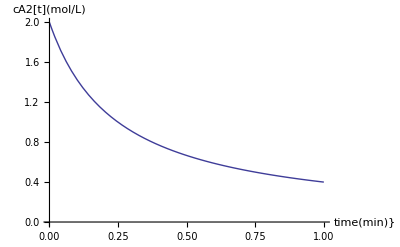

```mathematica
Plot[cA2[t],{t,0,1},PlotRange->{0,2},AxesLabel->{"time(min)}","cA2[t](mol/L)"}]
```

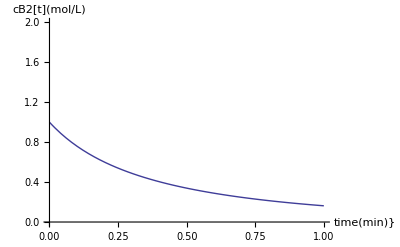

```mathematica
Plot[cB2[t],{t,0,1},PlotRange->{0,2},AxesLabel->{"time(min)}","cB2[t](mol/L)"}]
```

```mathematica
The steady state effluent concentrations in mol/L are therefore:
```

```mathematica
cA2[1]
```

0.4

```mathematica
cB2[1]
```

0.162474

```mathematica
Problem #3:
```

```mathematica
The rate expression is written:
```

```mathematica
Subscript[dc, A]/dt=-10^-2*cA^(1/2)
```

```mathematica
cA4in=0.0625 (* mol/L *);
```

```mathematica
cA40=cA4in(*mol/L *)
```

0.0625

```mathematica
80% conversion will occur when the concentration is (mol/L):
```

```mathematica
cA4crit=(1-.8)cA40
```

0.0125

```mathematica
ϵ=(3-1)/Abs[-1]
```

2

```mathematica
τ[fa_]=cA40*∫_0^fa 1/(10^-2((cA40(1-f))/(1+f*ϵ))^(1/2))ⅆf
```

ConditionalExpression[25. (1+(3 ArcSin[√(2/3)])/(√2)+(2 (-1+fa) √(1+2 fa)-3 √(2-2 fa) ArcSin[√(2/3) √(1-fa)])/(2 √((1-fa)/(1+2 fa)) √(1+2 fa))),(fa∉Reals&&(Re[1/fa]==0||Re[1/fa]≥1||2+Re[1/fa]≤0||1/fa∉Reals))||(Re[fa]<0&&1+2 Re[fa]>0&&(2+Re[1/fa]<0||1/fa∉Reals))||(Re[fa]<1&&Re[fa]>0&&(Re[1/fa]>1||1/fa∉Reals))]

```mathematica
τ  has units 1/s.
```

```mathematica
τ[.8]
```

37.8122

```mathematica
Problem #4:
```

```mathematica
The rate law for this system is given by:
```

```mathematica
Let acethane be representaldehyde be represented by A, methane be represented by B, and carbon monoxide be represented by C.
```

```mathematica
Subscript[dc, A]/dt=-k6*cA^2
```

```mathematica
Let the reactor vessel have a volume of 1L.
```

```mathematica
V=1 (* L *);
```

```mathematica
T=791(* K *);
```

```mathematica
P0=1(* atm *);
```

```mathematica
R=.082 (* atm-dm3/mol-K *)
```

0.082

```mathematica
ca50=P0/(R*T) (* mol/L *)
```

0.0154173

```mathematica
Giving the reactor pressure at a given time implies a certain extent of reaction as given by the ICE table.
```

```mathematica
{{□, A, B, C}, {I, 1, 0, 0}, {C, -x, +x, +x}, {E, 1-x, x, x}}
```

```mathematica
The sum of the E row will dictate the number of moles as a function of extent of reaction:
```

```mathematica
n[x_]=1-x+x+x
```

1+x

```mathematica
Solve[n[x]==1.5,x]
```

{{x→0.5}}

```mathematica
Therefore specifying that the number of moles increases by a factor of 1.5 correlates to an extent of reaction of .5 at 197 sec.
```

```mathematica
Converting to minutes:
```

```mathematica
N[197/60,3]
```

3.28

```mathematica
ϵ2=(2-1)/Abs[-1]
```

1

```mathematica
F=120 (*L/min*);
```

```mathematica
τ=197 (*1/sec*);
```

```mathematica
Integrate[(1/(1-xA))^2,{xA,0,.5}]
```

1.

```mathematica
Clear[k5]
```

```mathematica
Solve[τ==1/(ca50*k5),k5]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{k5→0.329249}}